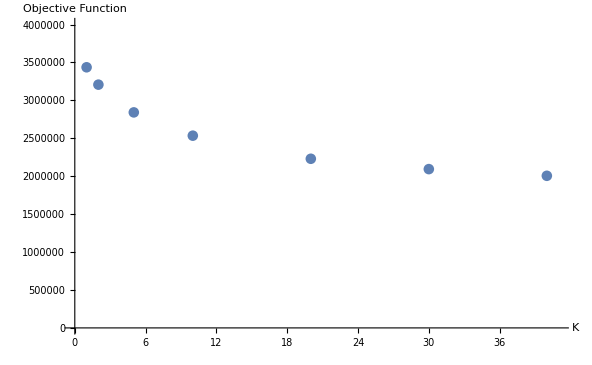

```mathematica
ListPlot[{{1,3436059.48417},{2,3207144.27033},{5,2841424.7295},{10,2534332.14383},{20,2229904.04117},{30,2093549.70417},{40,2005435.62817}},AxesLabel->{"K","Objective Function"},PlotRange->{{0,41},{0,4000000}}]
```

```mathematica
mat={8242546.9825,2800481.68767,2650575.812,2617240.2135,2601143.479,2590552.49033,2580775.731,2573734.19867,2568903.4525,2565221.92267,2562570.58483,2561064.0965,2559661.13833,2558022.82,2556092.99817,2554655.36983,2553664.75633,2553166.33833,2552693.27433,2552305.58733,2551438.8825,2550851.134,2550038.653,2549074.27817,2548160.11983,2547496.681,2546985.266,2546482.94633,2546145.80283,2545914.71867,2545759.988,2545612.86967,2545436.27217,2545344.69633,2545306.19617,2545269.91917,2545244.12517,2545213.07117,2545201.9505,2545199.65217,2545197.22883,2545194.99517,2545193.1105,2545183.80917,2545174.3145,2545155.71217,2545136.0685,2545120.36083,2545099.29017,2545081.05817,2545054.60617,2545021.67767,2545001.53633,2544982.7445,2544960.1845,2544946.3845,2544930.22533,2544924.54233};
```

```mathematica
For[i=1,i<Length[mat]+1,i++,mat[[i]]={i-1,mat[[i]]}]
```

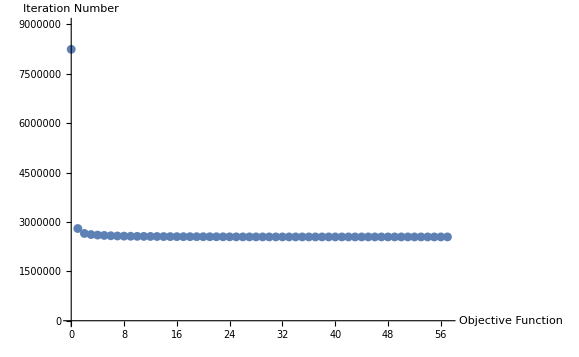

```mathematica
ListPlot[mat,PlotRange->{0,9000000},AxesLabel->{"Objective Function","Iteration Number"}]
```

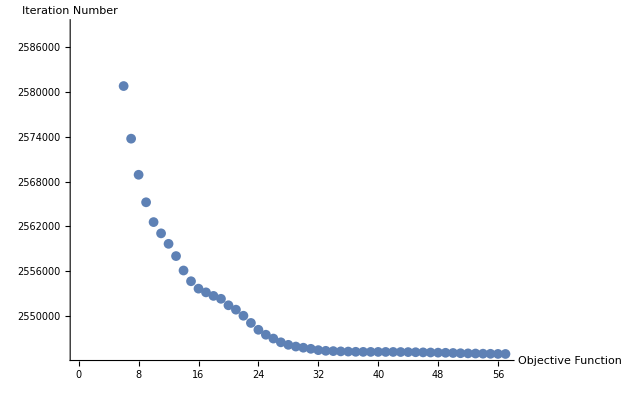

```mathematica
ListPlot[mat,AxesLabel->{"Objective Function","Iteration Number"}]
```